# Introduction to Mathematica

## #CA1 #Q2 Signals & Systems Mohammad GharehHasanloo

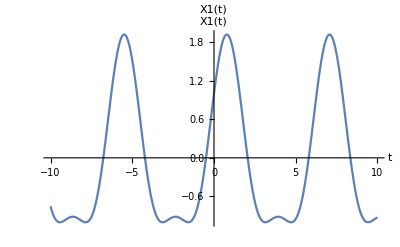

Cos[t]

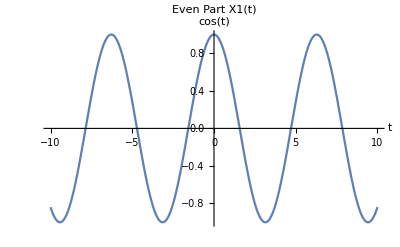

1/2 (2 Sin[t]+2 Cos[t] Sin[t])

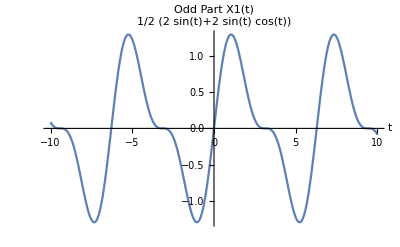

```mathematica
X1[t_]:=Cos[t]+Sin[t]+(Cos[t])*(Sin[t])
Plot[X1[t], {t,-10,10},PlotLabel->"X1(t)",AxesLabel->{"t","X1(t)"}]

EX1 = (X1[t]+X1[-t])/2
Plot[EX1,{t,-10,10},PlotLabel->"Even Part X1(t)",AxesLabel->{"t",EX1}]

OX1 = (X1[t]-X1[-t])/2
Plot[OX1,{t,-10,10},PlotLabel->"Odd Part X1(t)",AxesLabel->{"t",OX1}]
```

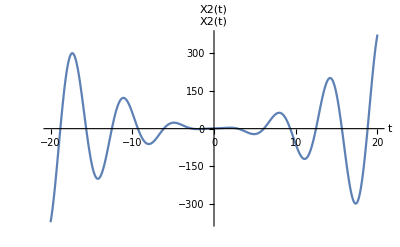

1

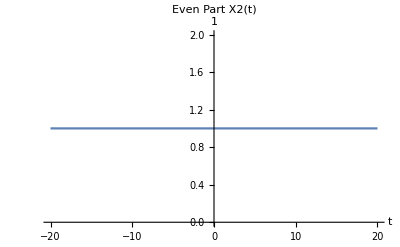

1/2 (2 t Cos[t]+2 t^2 Sin[t])

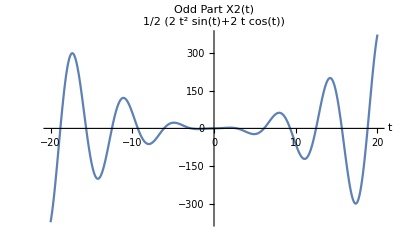

```mathematica
X2[t_]:=1+t*Cos[t]+(t^2)*Sin[t]
Plot[X2[t], {t,-20,20},PlotLabel->"X2(t)",AxesLabel->{"t","X2(t)"}]

EX2 = (X2[t]+X2[-t])/2
Plot[EX2,{t,-20,20},PlotLabel->"Even Part X2(t)",AxesLabel->{"t",EX2}]

OX2 = (X2[t]-X2[-t])/2
Plot[OX2,{t,-20,20},PlotLabel->"Odd Part X2(t)",AxesLabel->{"t",OX2}]
```

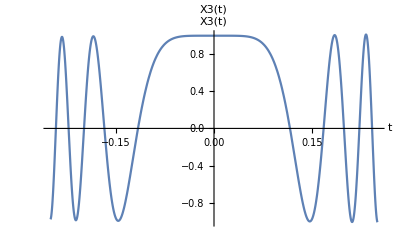

1/2 ((1-t^3) Cos[1000 t^3]+(1+t^3) Cos[1000 t^3])

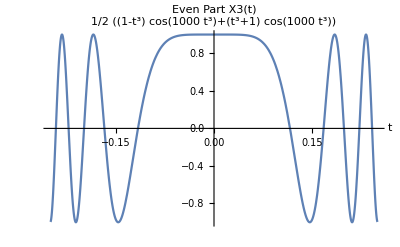

1/2 (-(1-t^3) Cos[1000 t^3]+(1+t^3) Cos[1000 t^3])

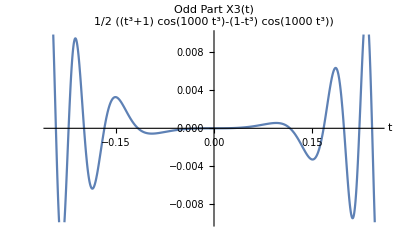

```mathematica
X3[t_]:=(1+t^3)*Cos[(10*t)^3]
Plot[X3[t], {t,-0.25,0.25},PlotLabel->"X3(t)",AxesLabel->{"t","X3(t)"}]

EX3 = (X3[t]+X3[-t])/2
Plot[EX3,{t,-0.25,0.25},PlotLabel->"Even Part X3(t)",AxesLabel->{"t",EX3}]

OX3 = (X3[t]-X3[-t])/2
Plot[OX3,{t,-0.25,0.25},PlotLabel->"Odd Part X3(t)",AxesLabel->{"t",OX3}]
```